```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/godfather/Documents/TaskDash/Flow

```mathematica
a = Import["out_data.txt","Table"][[4;;,2;;]]
```

{{0.,0.},{0.000287795,-0.83947},{0.000607589,-1.77165},{0.0009629,-2.8067},{0.00135771,-3.95589},{0.00179637,-5.23171},{0.00228378,-6.64796},{0.0028253,-8.21995},{0.00342702,-9.9646},{0.00409561,-11.9006},{0.00483848,-14.0487},{0.0056639,-16.4317},{0.00658101,-19.0747},{0.00760006,-22.0057},{0.00873228,-25.2553},{0.00999037,-28.8571},{0.0113882,-32.8483},{0.0129414,-37.2696},{0.0146671,-42.1656},{0.0165846,-47.5853},{0.0187152,-53.582},{0.0210824,-60.2138},{0.0237127,-67.5442},{0.0266352,-75.6417},{0.0298825,-84.5805},{0.0334906,-94.4403},{0.0374996,-105.306},{0.041954,-117.27},{0.0469034,-130.427},{0.0524027,-144.878},{0.058513,-160.728},{0.0653022,-178.083},{0.0728458,-197.051},{0.0812276,-217.737},{0.0905407,-240.24},{0.100889,-264.65},{0.112386,-291.039},{0.125161,-319.456},{0.139356,-349.912},{0.155128,-382.373},{0.172652,-416.737},{0.192123,-452.818},{0.213758,-490.311},{0.237797,-528.767},{0.264507,-567.539},{0.294184,-605.734},{0.327159,-642.144},{0.363798,-675.155},{0.404508,-702.644},{0.449741,-721.841},{0.5,-729.163},{0.550259,-721.74},{0.595492,-702.453},{0.636202,-674.883},{0.672841,-641.798},{0.705816,-605.323},{0.735493,-567.068},{0.762203,-528.242},{0.786242,-489.739},{0.807877,-452.202},{0.827348,-416.083},{0.844872,-381.683},{0.860644,-349.191},{0.874839,-318.706},{0.887614,-290.264},{0.899111,-263.852},{0.909459,-239.421},{0.918772,-216.899},{0.927154,-196.197},{0.934698,-177.213},{0.941487,-159.845},{0.947597,-143.983},{0.953097,-129.521},{0.958046,-116.354},{0.9625,-104.381},{0.966509,-93.5072},{0.970118,-83.6403},{0.973365,-74.695},{0.976287,-66.5917},{0.978918,-59.256},{0.981285,-52.6194},{0.983415,-46.6185},{0.985333,-41.195},{0.987059,-36.2955},{0.988612,-31.8711},{0.99001,-27.8771},{0.991268,-24.2727},{0.9924,-21.0209},{0.993419,-18.0879},{0.994336,-15.443},{0.995162,-13.0584},{0.995904,-10.9088},{0.996573,-8.97145},{0.997175,-7.2256},{0.997716,-5.65253},{0.998204,-4.2353},{0.998642,-2.95861},{0.999037,-1.80862},{0.999392,-0.772862},{0.999712,0.159955},{1.,1.}}

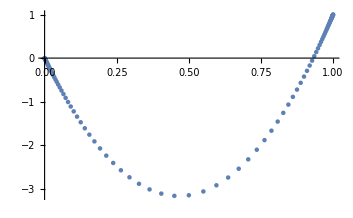

```mathematica
ListPlot[a]
```

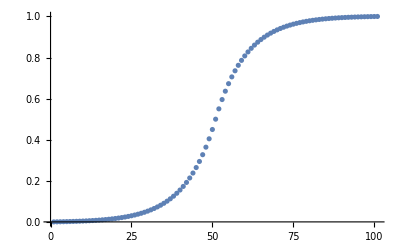

```mathematica
ListPlot[a[[;;,1]]]
```

```mathematica
A = Import["turb_out.txt","Table"]
```

{{0.,0.},{0.001,-2.69789},{0.00202299,-5.45179},{0.00314829,-8.47405},{0.00438611,-11.79},{0.00574772,-15.4273},{0.00724548,-19.4158},{0.00889303,-23.788},{0.0107053,-28.5793},{0.0126989,-33.8275},{0.0148917,-39.5739},{0.0173039,-45.8625},{0.0199573,-52.7409},{0.022876,-60.2598},{0.0260866,-68.4732},{0.0296183,-77.4387},{0.0335031,-87.2168},{0.0377764,-97.8712},{0.042477,-109.468},{0.0476477,-122.076},{0.0533355,-135.765},{0.059592,-150.606},{0.0664742,-166.667},{0.0740446,-184.015},{0.0823721,-202.714},{0.0915323,-222.815},{0.101609,-244.363},{0.112692,-267.382},{0.124885,-291.878},{0.138296,-317.825},{0.153049,-345.158},{0.169277,-373.764},{0.187127,-403.463},{0.206763,-433.997},{0.228362,-465.001},{0.252121,-495.985},{0.278257,-526.295},{0.307005,-555.073},{0.338629,-581.21},{0.373415,-603.276},{0.411679,-619.441},{0.45377,-627.386},{0.5,-624.211},{0.54623,-608.656},{0.588321,-584.073},{0.626585,-553.564},{0.661371,-519.622},{0.692995,-484.147},{0.721743,-448.498},{0.747879,-413.6},{0.771638,-380.046},{0.793237,-348.193},{0.812873,-318.232},{0.830723,-290.243},{0.846951,-264.229},{0.861704,-240.147},{0.875115,-217.922},{0.887308,-197.46},{0.898391,-178.658},{0.908468,-161.409},{0.917628,-145.605},{0.925955,-131.141},{0.933526,-117.914},{0.940408,-105.829},{0.946665,-94.7926},{0.952352,-84.7204},{0.957523,-75.5322},{0.962224,-67.1537},{0.966497,-59.5163},{0.970382,-52.5564},{0.973913,-46.2157},{0.977124,-40.4404},{0.980043,-35.1812},{0.982696,-30.3927},{0.985108,-26.0336},{0.987301,-22.0659},{0.989295,-18.4548},{0.991107,-15.1688},{0.992755,-12.1789},{0.994252,-9.45854},{0.995614,-6.9837},{0.996852,-4.73237},{0.997977,-2.68448},{0.999,-0.821764},{1.,1.}}

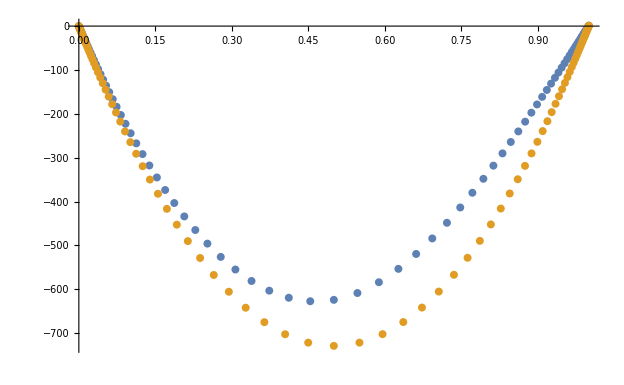

```mathematica
ListPlot[{A,a}]
```

```mathematica
a = Import["turb_out_plus.txt","Table"]
```

{{-Infinity,0.},{-8.9203,-0.000174301},{-8.22033,-0.000352705},{-7.78317,-0.000549074},{-7.45728,-0.000765253},{-7.19326,-0.00100329},{-6.96875,-0.00126545},{-6.77175,-0.00155429},{-6.59511,-0.00187263},{-6.43423,-0.00222368},{-6.28605,-0.00261104},{-6.14844,-0.00303884},{-6.01992,-0.00351181},{-5.89945,-0.00403547},{-5.78637,-0.00461635},{-5.68027,-0.0052623},{-5.58104,-0.00598303},{-5.48882,-0.00679088},{-5.40404,-0.00770213},{-5.32755,-0.0087392},{-5.2607,-0.00993463},{-5.20571,-0.0113388},{-5.16615,-0.0130359},{-5.14823,-0.0151821},{-5.16382,-0.0181094},{-5.2399,-0.0227001},{-5.46385,-0.032572},{-7.28252,-0.226748},{-5.18991,-0.030986},{-4.72185,-0.0209512},{-4.39463,-0.0157362},{-4.12568,-0.0118701},{-3.88882,-0.00843329},{-3.6723,-0.00503286},{-3.46983,-0.00144289},{-3.27761,0.00249962},{-3.09321,0.00693415},{-2.91493,0.0119949},{-2.74159,0.0178207},{-2.57227,0.0245623},{-2.4063,0.0323867},{-2.24314,0.0414825},{-2.08538,0.0522131},{-1.94512,0.0637026},{-1.82802,0.0746769},{-1.729,0.0850742},{-1.64433,0.0948623},{-1.57132,0.10403},{-1.5079,0.112582},{-1.45249,0.120532},{-1.40384,0.127902},{-1.36095,0.134717},{-1.32299,0.141007},{-1.2893,0.146802},{-1.25932,0.152133},{-1.23257,0.157031},{-1.20867,0.161525},{-1.18726,0.165645},{-1.16806,0.169419},{-1.15082,0.172873},{-1.13532,0.176032},{-1.12136,0.178919},{-1.10878,0.181557},{-1.09744,0.183965},{-1.0872,0.186164},{-1.07796,0.188169},{-1.0696,0.189999},{-1.06205,0.191666},{-1.05521,0.193187},{-1.04902,0.194572},{-1.04342,0.195834},{-1.03834,0.196984},{-1.03374,0.198031},{-1.02957,0.198984},{-1.02579,0.199852},{-1.02237,0.200642},{-1.01926,0.201361},{-1.01643,0.202015},{-1.01387,0.202611},{-1.01155,0.203153},{-1.00944,0.203646},{-1.00753,0.204094},{-1.00579,0.204502},{-1.00419,0.204869},{-1.00319,0.205344}}

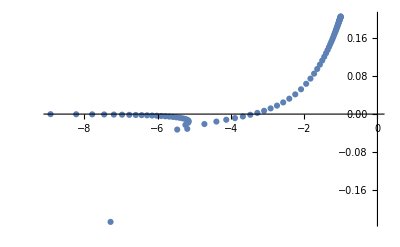

```mathematica
ListPlot[a]
```

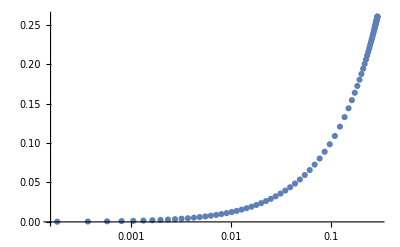

```mathematica
ListPlot[a, ScalingFunctions->{"Log",None}]
```